```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`;
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
(*https://mathematica.stackexchange.com/questions/18625/avoiding-grid-lines-inside-filled-area-in-regionplot-exported-as-pdf*)
```

```mathematica
db = DatabaseReference[FindFile[NotebookDirectory[]<>"/../data/genova.db"]]
```

DatabaseReference[…]

```mathematica
(* We select the absolute, treat F and T roads as the same. This simplifies graph and reduces computation time. Since data is bad anyways, I don't think this will affect the results by much.*)
queryGraphLinks = ExternalEvaluate[db, "
	WITH e(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	), g(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	)
	SELECT ABS(g.edge_id) as \"from\", ABS(e.edge_id) AS \"to\"
	FROM e
	INNER JOIN g
	WHERE e.node_to_id = g.node_from_id AND ABS(g.edge_id) <> ABS(e.edge_id)
	UNION
	SELECT ABS(e.edge_id) AS \"from\", ABS(g.edge_id) as \"to\"
	FROM e
	INNER JOIN geo_edges g
	WHERE e.node_from_id = g.node_to_id AND ABS(g.edge_id) <> ABS(e.edge_id)
;"];

(* We select max because we are interested on the study of the congested direction of the road*)
queryTrafficData = ExternalEvaluate[db, "
	SELECT
		g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
	FROM geo_edges g
	INNER JOIN traffic_data t
	ON g.edge_id = ABS(t.edge_id)
	WHERE t.hour_slot = 170
	GROUP BY g.edge_id
;"];
```

ExternalEvaluate::unknownSys: DatabaseReference[<|Backend→SQLite,Name→C:\Users\Matteo\Desktop\repo\bazz\data\genova.db|>] is not a known system in the ExternalEvaluate Framework.

```mathematica
graphLinks = Thread[#["from"]<-> #["to"] /. #]&/@Normal[queryGraphLinks];
g=Graph[graphLinks,VertexLabels->None];
validNodes = queryTrafficData[[;;, 1]];
invalidNodes = Select[VertexList[g], !MemberQ[validNodes, #]&];
g = VertexDelete[g, invalidNodes];
disconnectedNodes = Flatten[ConnectedComponents[g][[2;;]]]; (* Remove disconnected train network *)
g = VertexDelete[g, disconnectedNodes];
```

```mathematica
Rasterize[GraphPlot[g], RasterSize->1000]
```

-Graphics-

```mathematica
Count[VertexDegree[g], 2] (* Are there relatively few nodes with only two degrees? Can we go on without simplifying the graph? *)
```

530

## Getting transition rates

```mathematica
ToAssociations = ResourceFunction["ToAssociations"];
neighborsOf = ToAssociations[# ->VertexList@VertexDelete[NeighborhoodGraph[g, #], #] &/@ VertexList[g]];
carCount =ToAssociations[ #["edge_id"]->#["count"]&/@ Normal[queryTrafficData]];
```

```mathematica
neighborsOf[55262035]
carCount[55262035]
```

{55262034,55262068}

0.193548

### Random walk

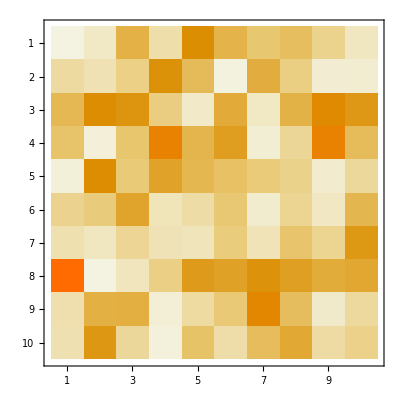
{-Graphics-,-Graphics-}

{0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228,0.316228}

{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}

```mathematica
n = 10;
t = 100;
agentCount=20;
MarkovMatrix[n_,min_:0]:=If[min n<1,Transpose@RandomPoint[Simplex[IdentityMatrix[n](1-min n)],n]+min,$Failed];
markovMatrix = MarkovMatrix[n];
{markovMatrix // MatrixPlot, g = WeightedAdjacencyGraph[markovMatrix]}
statDist = Re /@ N[Eigenvectors[markovMatrix // Transpose][[1]]]
statDist /= Total[statDist]
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

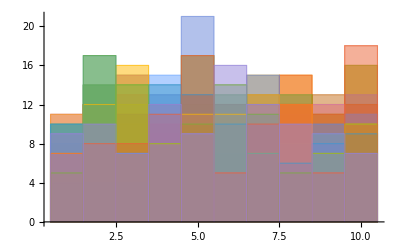

```mathematica
proc = DiscreteMarkovProcess[statDist // Flatten, markovMatrix];
data = RandomFunction[proc, {0, t}, agentCount];
Histogram[data]
```

For a left stochastic matrix, each column sums to 1.  Values are the probability of moving from node=column to node=row.

Algorithm:
1) Move each agent
2) Check if any node fails
3) immediately, redistribute agents, propagate avalanche
4) End simulaiton

```mathematica
Needs["OpenCLLink`"]
CUDAInformation[]
result["LibrariesLoaded"]
```

{1→{Name→NVIDIA GeForce GTX 970,Clock Rate→1228000,Compute Capabilities→5.2,GPU Overlap→1,Maximum Block Dimensions→{1024,1024,64},Maximum Grid Dimensions→{2147483647,65535,65535},Maximum Threads Per Block→1024,Maximum Shared Memory Per Block→49152,Total Constant Memory→65536,Warp Size→32,Maximum Pitch→2147483647,Maximum Registers Per Block→65536,Texture Alignment→512,Multiprocessor Count→13,Core Count→1664,Execution Timeout→1,Integrated→False,Can Map Host Memory→True,Compute Mode→Default,Texture1D Width→65536,Texture2D Width→65536,Texture2D Height→65536,Texture3D Width→4096,Texture3D Height→4096,Texture3D Depth→4096,Texture2D Array Width→16384,Texture2D Array Height→16384,Texture2D Array Slices→2048,Surface Alignment→512,Concurrent Kernels→True,ECC Enabled→False,TCC Enabled→False,Total Memory→4294836224}}

Missing[NotAvailable,LibrariesLoaded]

```mathematica
$OpenCLPlatform
```

Automatic

```mathematica
GPUArray[{1, 2}]
GPU
```

GPUArray::nogpu: No supported GPUs were detected on the system.

{1,2}

GPU

## Fundamental Diagram

```mathematica
GetSpeedAndDensityOfSingleRoad = (edgeId) ↦ Module[{queryNodeCapacity, fluxValues, densityValues},
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
fluxValues = Normal@Transpose[queryNodeCapacity]["flux"];
densityValues = Normal@Transpose[queryNodeCapacity]["density"];

{densityValues, fluxValues} // Transpose
];

PlotCongestionOfSingleRoad = (edgeId) ↦ Module[{},
ListPlot[GetSpeedAndDensityOfSingleRoad[edgeId], PlotRange->All]
];
```

```mathematica
testRoad = GetSpeedAndDensityOfSingleRoad[55255453];
ListLinePlot[testRoad[[;;, 1]]]
ListLinePlot[testRoad[[;;, 2]]]
ListPlot[testRoad]
```

ExternalEvaluate::unknownSys: DatabaseReference[<|Backend→SQLite,Name→C:\Users\Matteo\Desktop\repo\bazz\data\genova.db|>] is not a known system in the ExternalEvaluate Framework.

-Graphics-

Part::partw: Part 2 of ExternalEvaluate[density] does not exist.

ExternalEvaluate::unknownSys: DatabaseReference[<|Backend→SQLite,Name→C:\Users\Matteo\Desktop\repo\bazz\data\genova.db|>] is not a known system in the ExternalEvaluate Framework.

General::stop: Further output of ExternalEvaluate::unknownSys will be suppressed during this calculation.

Part::partw: Part 2 of ExternalEvaluate[density] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: {ExternalEvaluate[density],ExternalEvaluate[DatabaseReference[<|Backend→SQLite,Name→C:\Users\Matteo\Desktop\repo\bazz\data\genova.db|>],
		SELECT
			t.hour_slo…	GROUP BY t.hour_slot
	;]^T[flux]}⟦1;;All,2⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[{Transpose[ExternalEvaluate[DatabaseReference[…],
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = 55255453
		GROUP BY t.hour_slot
	;]][density],Transpose[ExternalEvaluate[DatabaseReference[…],
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = 55255453
		GROUP BY t.hour_slot
	;]][flux]}⟦1;;All,2⟧]

ExternalEvaluate::unknownSys: DatabaseReference[<|Backend→SQLite,Name→C:\Users\Matteo\Desktop\repo\bazz\data\genova.db|>] is not a known system in the ExternalEvaluate Framework.

General::stop: Further output of ExternalEvaluate::unknownSys will be suppressed during this calculation.

-Graphics-

```mathematica
validNodes = VertexList[g];
$DefaultParallelKernels= {8};
CloseKernels[]
LaunchKernels[];
heatmapPoints = ParallelMap[GetSpeedAndDensityOfSingleRoad, validNodes, Method->"ItemsPerEvaluation" -> 10];
```

```mathematica
Export["heatmapPoints.mx", heatmapPoints];
```

```mathematica
heatmapPoints = Import["C:\\Users\\Matteo\\Documents\\heatmapPoints.mx"];
```

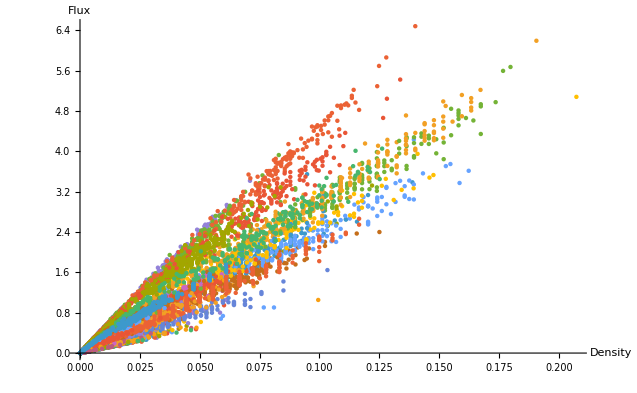

```mathematica
ListPlot[heatmapPoints[[200;;500]], AxesLabel->{"Density", "Flux"}, PlotStyle->PointSize[.005], PlotRange->Full]
```